# STAT 333 Assignment 2

```mathematica
problem 1
```

```mathematica
In 1, 000 Bernoulli experiments, the sample mean x_bar = p_hat = 0.48.Calculate
the confidence level of the interval 0.48 ± 0.03.
```

```mathematica
p=0.48;
```

```mathematica
sd = √(p*(1-p))
```

0.4996

```mathematica
z = 0.03*√1000/sd
```

1.89889

As we look at the normal distribution table, we get the following:

```mathematica
α = 2(1- 0.9713)
```

0.0574

```mathematica
confidence_level = 1- α
```

0.9426

```mathematica
Problem 2
```

```mathematica
For the same experiments,calculate the size of the confidence interval
given the confidence level 0.95.
```

```mathematica
α' = 0.95/2
```

0.475

As we look at the normal distribution table, we get that z =1.96

```mathematica
ME = 1.96*sd/√1000
```

0.0309655

```mathematica
interval_size= ME*2
```

0.061931

```mathematica
problem 3
```

```mathematica
Find the number n of Bernoulli experiments needed to obtain for p a
confidence interval of size 0.02  at confidence level 0.99.
```

As we look at the normal distribution table, we get that z= 2.57

```mathematica
n = p(1-p)(2.57/0.01)^2
```

16485.8

```mathematica
problem 4
```

```mathematica
Random quantity X has the Laplace density fx(x;µ,s)=ce^(-|x-µ l/s)
defined on the whole real line.Calculate c.Using Mathematica,graph
this probability d.f.for different values of parameters µ and s>0,and the
corresponding cumulative d.f.Fx(x;µ,s). Calculate the mean,variance,and the nth moment of X using the gamma-function calculus.
```

We have that c = 1/(2 s) from the first moment. The following is the calculation:
1 = c µ^0 s^1(0
0)(0!+0!) = c*s*2, which implies that c = 1/(2s)

```mathematica
pdf1 = Plot[Table[PDF[LaplaceDistribution[2,β],x],{β,{0.5,1,2}}]//Evaluate,{x,0,5},PlotRange->All];
```

```mathematica
pdf2 = Plot[Table[PDF[LaplaceDistribution[β,2],x],{β,{0.5,1,2}}]//Evaluate,{x,0,5},PlotRange->All];
pdf3 = Plot[Table[PDF[LaplaceDistribution[β,1],x],{β,{0.5,1,2}}]//Evaluate,{x,0,5},PlotRange->All];
pdf4 = Plot[Table[PDF[LaplaceDistribution[β,0.5],x],{β,{0.5,1,2}}]//Evaluate,{x,0,5},PlotRange->All];
```

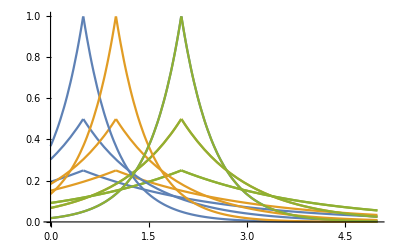

```mathematica
Show[pdf1,pdf2,pdf3,pdf4]
```

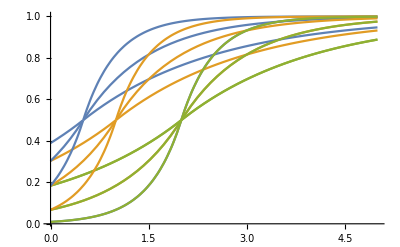

```mathematica
cdf1=Plot[Table[CDF[LaplaceDistribution[2,β],x],{β,{0.5,1,2}}]//Evaluate,{x,0,5},PlotRange->All];
cdf2 = Plot[Table[CDF[LaplaceDistribution[β,2],x],{β,{0.5,1,2}}]//Evaluate,{x,0,5},PlotRange->All];
cdf3 = Plot[Table[CDF[LaplaceDistribution[β,1],x],{β,{0.5,1,2}}]//Evaluate,{x,0,5},PlotRange->All];
cdf4 = Plot[Table[CDF[LaplaceDistribution[β,0.5],x],{β,{0.5,1,2}}]//Evaluate,{x,0,5},PlotRange->All];
Show[cdf1,cdf2,cdf3,cdf4]
```

From the Gramma function, we can get the following results: 
mean = µ_1= 1/(2s)µ s (1
0)(0!+0!) = µ
variance =EX^2- (EX)^2=µ_2-(µ_1)^2=  2 s^2+µ^2-µ^2 = 2 s^2
nth- moment = ∫_(-∞)^∞ x^n f(x)ⅆx = ∫_(-∞)^∞ x^n c e^(-(|x-µ|)/s)ⅆx  =1/2 ∑_(j=0)^n (n
j)µ^(n-j)s^j(j!+(-1)^j j!)

```mathematica
problem 5
```

```mathematica
Simulate a random sample of size n=1000 with an exponential distribution
and plot its histogram against the exponential density. Verify the Law
of Large Numbers and the Stability of Fluctuations Law for these data.Use UVW and/or Statistics packages
```

```mathematica
arr=Table[Random[ExponentialDistribution[1]],{1000}];
```

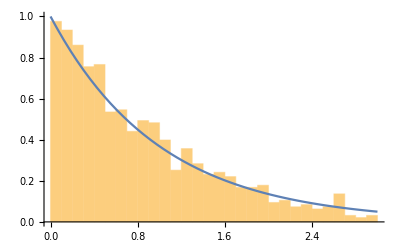

```mathematica
Show[Histogram[arr,{0,3,0.1},"PDF"],Plot[PDF[ExponentialDistribution[1],x],{x,0,3},PlotRange->{0,5}]]
```

```mathematica
cdf[x_,n_]:=Sum[If[arr[[i]]<x,1,0]/n,{i,1,n}]
```

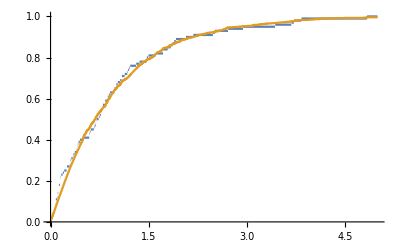

```mathematica
Plot[{cdf[x,100] ,cdf[x,1000]},{x,0,5}]
```

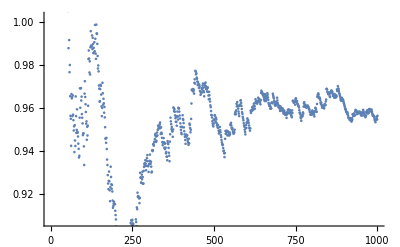

```mathematica
LLN1=Table[Accumulate[arr][[n]]/n,{n,1,1000 }] ; 
ListPlot[LLN1]
```

```mathematica
LargeNumbers[listofdata_List,opts___] :=
  Block[
    {listofmeans,len},

    listofmeans = Rest[FoldList[Plus,0.,listofdata]];
    len=Length[listofdata];
    listofmeans = listofmeans / Range[len];

    ListPlot[listofmeans , 

	     PlotRange -> All,
	     Prolog    -> PointSize[0.001],
	     opts
	    ]
       ]
LargeNumbers[arr]
```

-Graphics-

```mathematica
UVWHistogram[listofdata_List,listofbounds_List,opts___]:=

    Block[{list,nbclasses,cardinal,i,ordinates,abscissas,g},

       list = Cases[listofdata,
			x_/;First[listofbounds]<x<Last[listofbounds]];
       nbclasses = Length[listofbounds]-1;

       cardinal = Table[Length[Select[list,
				listofbounds[[i]]<#<=listofbounds[[i+1]] &]],
			  {i,1,nbclasses}];

       cardinal = cardinal / (Drop[listofbounds,1]
				  - Drop[listofbounds,-1]);
       cardinal = cardinal / Length[list];

       ordinates = Flatten[Transpose[{cardinal,cardinal,
				      Table[0,{nbclasses}]}]];
       
       
       abscissas = Flatten[Transpose[{Drop[listofbounds,-1],
					  Drop[listofbounds,1],
					      Drop[listofbounds,1]}]];
       
       g = Transpose[{abscissas,ordinates}];
       g = Prepend[g,{First[listofbounds],0}];

       ListPlot[g,
		 opts,
		 PlotRange  -> All,
		 PlotJoined -> True]
    ]


RegularHisto[listofdata_List,xmin_,xmax_,nx_,opts___]:=

  Block[{cardinal,list,step,i,abscissas,ordinates,g},

	step  = N[(xmax-xmin)/nx];

	list = Cases[listofdata,x_/;xmin<x<xmax];
	list = list - xmin;
	list = list/step;
	list = Ceiling[list];

	cardinal=Table[Count[list,i],{i,1,nx}];
	cardinal=cardinal / (step*Length[list]);

	ordinates = Flatten[Transpose[{cardinal,cardinal,Table[0,{nx}]}]];
	abscissas = Flatten[Transpose[{Range[xmin,xmax-step,step],
					    Range[xmin+step,xmax,step],
					    Range[xmin+step,xmax,step]}]]; 
						 
	g = Transpose[{abscissas,ordinates}];                                         
	g = Prepend[g,{xmin,0}];
     

	ListPlot[g, 
		    opts,
		    PlotJoined -> True,
		    PlotRange  -> All ]

	]

CentralLimit[ listofdata_List,mu_,sigma_,n_,opts___] :=
  Block[
    {listpart, max,min,g1,g2},
   
    listpart = Transpose[Partition[listofdata,n]];
    listpart = Apply[Plus,listpart];
    listpart = listpart - (N[n] mu);
    listpart = listpart/(Sqrt[N[n]] sigma);
    
    min = Min[listpart];
    max = Max[listpart];
   
    g1 := RegularHisto[listpart,min,max,20,
		   DisplayFunction -> Identity];

    g2 := Plot[Exp[-(x^2)/2] / Sqrt[2 Pi], {x,min,max},
		   DisplayFunction -> Identity];
    Show[g1,g2,DisplayFunction->$DisplayFunction]
    ]
```

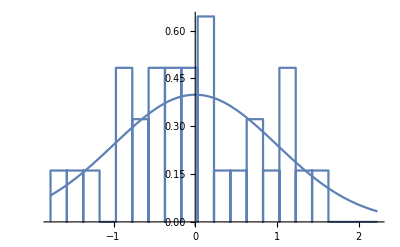

```mathematica
n=30;
mu=Mean[arr];
sigma=StandardDeviation[arr];
CentralLimit[arr,Mean[arr],StandardDeviation[arr],n]
```

Function[x,(ⅇ^(-x^2/2))/(√(2 π))]

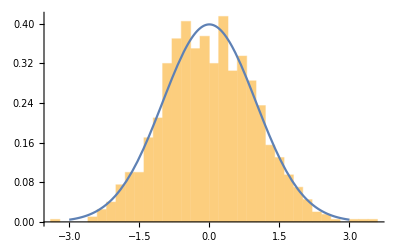

```mathematica
arr2={};
For [i=0,i<1000,i++,SeedRandom[i+1112];
arr3=RandomVariate[ExponentialDistribution[1],1000];
arr2=Join[arr2,{Mean[arr3]-1}*√1000]]
normal=PDF[NormalDistribution[0,1]]
Show[Histogram[arr2,Automatic,"PDF"],Plot[normal[x],{x,-3,3}]]
```